```mathematica
Y[r_]=(∫_0^(2/u) ((c (2/c-u)^2) (Hypergeometric0F1[3,-(2/c-u) (c^2-2 r c+r^2)]-Hypergeometric0F1[3,-(2/c-u) (c^2+r^2+2 cr)]))/r ⅆc)/(8 π^2)
```

```mathematica
Plot[(∫_0^(2/u) ((c (2/c-u)^2) (Hypergeometric0F1[3,-(2/c-u) (c^2-2 r c+r^2)]-Hypergeometric0F1[3,-(2/c-u) (c^2+r^2+2 cr)]))/r ⅆc)/(8 π^2)*4Pi r^2,{r,0,10}]
```

```mathematica
Limit[Sum[((c (2/c-0.164414)^2) (Hypergeometric0F1[3,-(2/c-0.164414) (c^2-2 r c+r^2)]-Hypergeometric0F1[3,-(2/c-0.164414) (c^2+r^2+2 cr)]))/(8 π^2 r)HeavisideTheta[2/c-0.164414],{c,0,Infinity,d}],d->0]
```

lim_(d→0) Sum[1/(8 π^2 r)(-0.164414+2/c)^2 c HeavisideTheta[-0.164414+2/c] (-Hypergeometric0F1[3,(0.164414-2/c) (c^2+2 cr+r^2)]+Hypergeometric0F1[3,(0.164414-2/c) (c^2-2 c r+r^2)]),{c,0,∞,d}]

```mathematica
J[r_]=Integrate[(0.0003423638159323836 (12.16441422263311-1c)^2 (Hypergeometric0F1[3,(0.164414-2/c) (c-r)^2]-Hypergeometric0F1[3,(0.164414-2/c) (c+r)^2]))/(c r),{c,0,2/0.164414}]
```

$Aborted

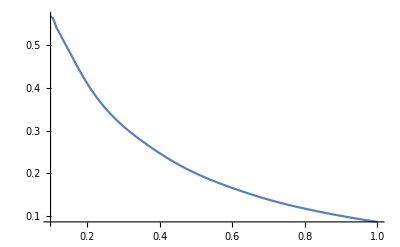

```mathematica
Plot[Sum[((c (2/c-0.164414)^2) (Hypergeometric0F1[3,-(2/c-0.164414) (c^2-2 r c+r^2)]-Hypergeometric0F1[3,-(2/c-0.164414) (c^2+r^2+2 c r)]))/(100 8 π^2 r),{c,0.0001,2/0.164414,1/100}],{r,0.1,1}]
```

```mathematica
Plot[Sum[1/(8 π^2 r)(c (2/Max[c,0.0001]-0.164414)^2) (Hypergeometric0F1[3,-(2/Max[c,0.0001]-0.164414) (c^2-2 r c+r^2)]-Hypergeometric0F1[3,-(2/Max[c,0.0001]-0.164414) (c^2+r^2+2 cr)]),{c,0,2/0.164414,0.0001}],{r,0,1}]
```

```mathematica
Simplify[((c (2/c-0.164414)^2) (Hypergeometric0F1[3,-(2/c-0.164414) (c^2-2 r c+r^2)]-Hypergeometric0F1[3,-(2/c-0.164414) (c^2+r^2+2 c r)]))/(8 π^2 r)]
```

```mathematica
(0.0003423638159323836 (12.16441422263311-1. c)^2 (Hypergeometric0F1[3,(0.164414-2/c) (c-r)^2]-1. Hypergeometric0F1[3,(0.164414-2/c) (c+r)^2]))/(c r)
```

```mathematica
Hypergeometric0F1[3,(0.164414-2/c) (c+r)^2]
```

Hypergeometric0F1[3,(0.164414-2/c) (c+r)^2]

```mathematica
G[r_]=Integrate[(x(-0.164414+2/x)/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-0.164414+2/x]]-x(-0.164414+2/x)/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-0.164414+2/x]])HeavisideTheta[-0.164414+2/x],{x,0,2/0.164414}]/(8Pi^2)
```

(∫_0^12.1644 (((-0.164414+2/x) x BesselJ[2,2 √(-0.164414+2/x) (-r+x)])/(-r+x)^2-((-0.164414+2/x) x BesselJ[2,2 √(-0.164414+2/x) (r+x)])/(r+x)^2) HeavisideTheta[-0.164414+2/x]ⅆx)/(8 π^2)

```mathematica
Simplify[(∫_0^12.16441422263311 (((-0.164414+2/x) x BesselJ[2,2 √(-0.164414+2/x) (-r+x)])/(-r+x)^2-((-0.164414+2/x) x BesselJ[2,2 √(-0.164414+2/x) (r+x)])/(r+x)^2)ⅆx)/(8 π^2)]
```

$Aborted

```mathematica
Plot[G[r],{r,0.05,0.1}]
```

```mathematica
Sum[(x(-0.164414+2/(x+0.0001))/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-0.164414+2/(x+0.0001)]]-x(-0.164414+2/(x+0.0001))/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-0.164414+2/(x+0.0001)]])HeavisideTheta[-0.164414+2/(x+0.0001)],{x,0,(2/0.164414)-0.0001,0.0001}]/(8Pi^2)
```

(0.+(0.999984 BesselJ[2,19 1])/(0.0001-r)^2+1/1^2+364927)/(8 π^2)
 |  |  |  |

```mathematica
Plot[Sum[(x(-0.164414+2/Max[x,0.001])/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-0.164414+2/Max[x,0.001]]]-x(-0.164414+2/Max[x,0.001])/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-0.164414+2/Max[x,0.001]]])r/(2Pi),{x,0,(2/0.164414),0.001}]/(8Pi^2),{r,0,20}]
```

$Aborted

```mathematica
o
```

```mathematica
Integrate[((-u+2/c)^n)*((c-r)^n-(c+r)^n),{c,0,2/u}]
```

$Aborted

```mathematica
Plot[Sum[(0.001)(x(-0.164414+2/Max[x,0.0001])/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-0.164414+2/Max[x,0.0001]]]-x(-0.164414+2/Max[x,0.0001])/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-0.164414+2/Max[x,0.0001]]])/(8r Pi^2),{x,0,(2/0.164414),0.0001}],{r,0,10}]
```

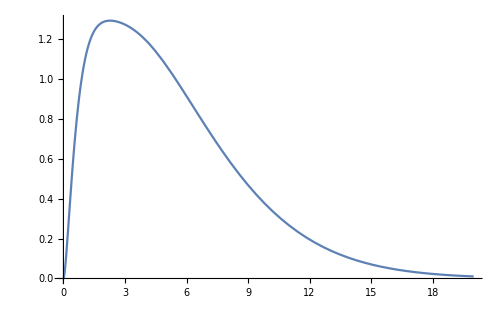

```mathematica
Plot[2Sum[((-0.164414x+2)/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-0.164414+2/x]]-(-0.164414x+2)/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-0.164414+2/x]])r/(2Pi)*(0.001),{x,0,(2/0.164414),0.001}],{r,0,20}]
```

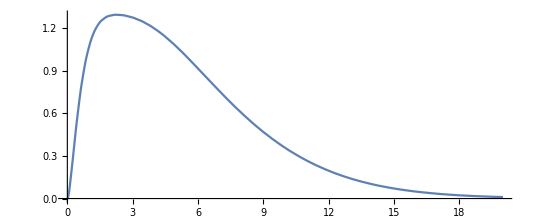

```mathematica
Show[%1,ImageSize->{533,221},AspectRatio->Full]
```

```mathematica
BesselJ[3,Infinity]
```

0

```mathematica
Integrate[((-0.164414x+2)/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-0.164414+2/x]]-(-0.164414x+2)/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-0.164414+2/x]])r/(2Pi),{x,0,(2/0.164414)}]
```

∫_0^12.1644 (r (((2-0.164414 x) BesselJ[2,2 √(-0.164414+2/x) (-r+x)])/(-r+x)^2-((2-0.164414 x) BesselJ[2,2 √(-0.164414+2/x) (r+x)])/(r+x)^2))/(2 π)ⅆx

```mathematica
Plot[∫_0^12.16441422263311 (r (((2-0.164414 x) BesselJ[2,2 √(-0.164414+2/x) (-r+x)])/(-r+x)^2-((2-0.164414 x) BesselJ[2,2 √(-0.164414+2/x) (r+x)])/(r+x)^2))/(2 π)ⅆx,{r,0,1}]
```

$Aborted

(0.0000253303 ((1.99984 BesselJ[2,89.439 1])/(0.001-r)^2-(1.99984 BesselJ[2,1])/(1)^2))/r+(0.0000253303 (1/1^2-1/1))/r+(0.0000253303 1)/r+1/r+12157+1/r+1/r+(0.0000253303 (1))/r+(0.0000253303 ((2. BesselJ[2,15])/(1)^2-(2. 1)/1^2))/r
 |  |  |  |

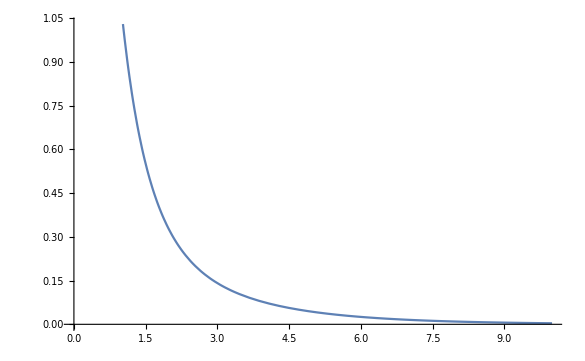

```mathematica
Plot[Sum[((-0.164414x+2)/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-0.164414+2/x]]-(-0.164414x+2)/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-0.164414+2/x]])/(r Pi)*(0.001),{x,0,(2/0.164414),0.001}],{r,0,10}]
```

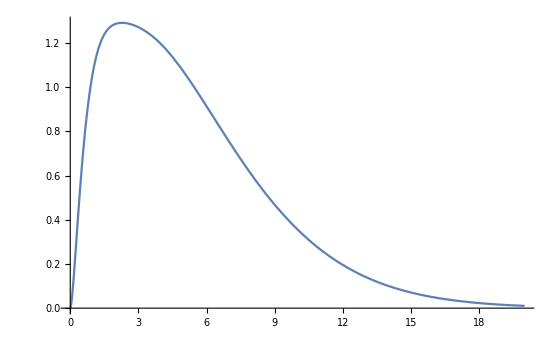

```mathematica
Plot[Sum[((-0.164414x+2)/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-0.164414+2/x]]-(-0.164414x+2)/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-0.164414+2/x]])r/( Pi)*(0.001),{x,0,(2/0.164414),0.001}],{r,0,20}]
```

```mathematica
S[r_]=Sum[((-0.164414x+2)/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-0.164414+2/x]]-(-0.164414x+2)/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-0.164414+2/x]])/(r Pi)*(0.001),{x,0,(2/0.164414),0.001}]
```

(0.00031831 ((1.99984 BesselJ[2,89.439 1])/(0.001-r)^2-(1.99984 BesselJ[2,1])/(1)^2))/r+(0.00031831 (1.9996711/1^2-1))/r+(0.00031831 1)/r+1/r+12157+1/r+1/r+(0.00031831 (1))/r+(0.00031831 ((2. BesselJ[2,15])/(1)^2-(2. 1)/1^2))/r
 |  |  |  |

```mathematica
S̄[r_]=S[r]*r^2
```

r^2 ((0.00031831 ((1.99984 BesselJ[2,89.439 1])/(0.001-r)^2-(1.99984 BesselJ[2,1])/(1)^2))/r+(0.00031831 (1/1^2-1))/r+(0.00031831 1)/r+12159+1/r+(0.00031831 (1-1))/r+(0.00031831 ((2. BesselJ[2,15])/(1)^2-(2. 1)/1^2))/r)
 |  |  |  |

```mathematica
Subscript[S̄, u][r_,u_]=Sum[((-u x+2)/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-u+2/x]]-(-u x+2)/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-u+2/x]])r/( Pi)*(0.001),{x,0,(2/u),0.001}]
```

Sum[0.00031831 r (((2-u x) BesselJ[2,2 √(-u+2/x) (-r+x)])/(-r+x)^2-((2-u x) BesselJ[2,2 √(-u+2/x) (r+x)])/(r+x)^2),{x,0,2/u,0.001}]

```mathematica
Solve[Sum[Sum[((-u x+2)/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-u+2/x]]-(-u x+2)/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-u+2/x]])r/( Pi)*(0.01),{x,0,(2/u),0.01}],{r,0,Infinity,0.01}]==10,0.1<u<0.2]
```

$Aborted

```mathematica
Solve[Sum[Sum[((-u x+2)/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-u+2/x]]-(-u x+2)/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-u+2/x]])r/( Pi)*(0.001),{x,0,(2/u),0.001}],{r,0,Infinity,0.001}]==2,u]
```

```mathematica
Solve[Sum[Sum[((-u x+2)/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-u+2/x]]-(-u x+2)/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-u+2/x]])r/( Pi)*(0.001),{x,0,(2/u),0.001}],{r,0,Infinity,0.001}]==28,u]
```

```mathematica
NSum[Sum[((-0.164414 x+2)/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-0.164414+2/x]]-(-0.164414 x+2)/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-0.164414+2/x]])r/( Pi)*(0.01),{x,0,(2/0.164414),0.01}],{r,0,100,0.01}]
```

```mathematica
Subscript[Y, 10]=Table[Sum[(0.01 (((2-0.2 x) 22 (x-r) √(2/x-0.2))/(x-r)^2-((2-0.2 x) 22 (r+x) √(2/x-0.2))/(r+x)^2))/(r π),{x,0.00000000001,2/0.2,0.01}],{r,0.25,10,0.5}]
```

{4.33946,1.51935,0.709584,0.383341,0.229926,0.148593,0.101117,0.0712682,0.0513177,0.0374996,0.0276828,0.0205693,0.0153542,0.0114992,0.00864048,0.00650383,0.00490334,0.00370328,0.00279578,0.00210957}

```mathematica
Sum[(0.01 (((2-0.164414 x) 22 (x-r) √(2/x-0.164414))/(x-r)^2-((2-0.164414 x) 22 (r+x) √(2/x-0.164414))/(r+x)^2))/(π r),{x,0,2/0.164414,0.01}]
```

```mathematica
Sum[(0.01 (((2-0.164414 x) 22 (x-0.1) √(2/x-0.164414))/(x-0.1)^2-((2-0.164414 x) 22 (0.1+x) √(2/x-0.164414))/(0.1+x)^2))/(0.1 π),{x,0.005,10,0.01}]
```

7.72253

```mathematica
4Pi((Sqrt[-0.164414+2/r])^3)*HeavisideTheta[-0.164414+2/r]/(3Pi^2)
```

(4 (-0.164414+2/r)^(3/2) HeavisideTheta[-0.164414+2/r])/(3 π)

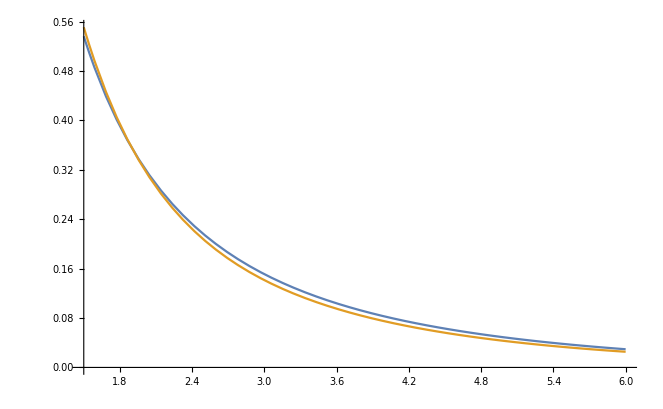

```mathematica
Plot[{(4 (-0.164414+2/r)^(3/2) HeavisideTheta[-0.164414+2/r])/(3 π),Sum[((-0.164414x+2)/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-0.164414+2/x]]-(-0.164414x+2)/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-0.164414+2/x]])/(r Pi)*(0.001),{x,0,(2/0.164414),0.001}]},{r,1.5,6}]
```

```mathematica
Table[(4(-0.164414+2/Max[r,0.25])^(3/2) HeavisideTheta[-0.164414+2/Max[r,0.25]])/(3 π),{r,0,2,0.5}]
```

{9.30885,3.18813,1.05548,0.536371,0.324172}

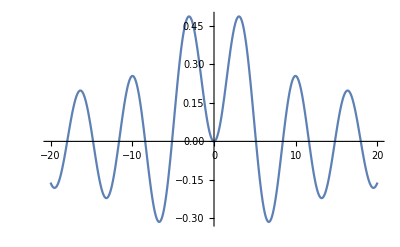

```mathematica
Plot[{BesselJ[2,x]},{x,-20,20}]
```

```mathematica
Table[Sum[((-0.164414x+2)/((x-r)^2)*BesselJ[2,2(x-r)Sqrt[-0.164414+2/Max[0.25,x]]]-(-0.164414x+2)/((x+r)^2)*BesselJ[2,2(x+r)Sqrt[-0.164414+2/Max[0.25,x]]])/(r Pi)*(0.001),{x,0,(2/0.164414),0.001}],{r,0.25,5,0.25}]
```

```mathematica
Subscript[n, 3][r_]=∫_({a,t}∈ImplicitRegion[(2/u)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&-1≤t≤1,{a,t}]) (BesselJ[3,2 a √(-u+2/(√(a^2+r^2-2 a r t)))] (-u+2/(√(a^2+r^2-2 a r t)))^(3/2))/(2 a π^2)
```

$Aborted

```mathematica
Subscript[n̄, 3][r_]=Subscript[n, 3][r]4Pi^2
```

```mathematica
Solve[Integrate[∫_({a,t}∈ImplicitRegion[(2/u)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&-1≤t≤1,{a,t}]) (BesselJ[3,2 a √(-u+2/(√(a^2+r^2-2 a r t)))] (-u+2/(√(a^2+r^2-2 a r t)))^(3/2))/(2 a π^2)*4Pi r^2,{r,0,Infinity}]==10,u]
```

```mathematica
Solve[Integrate[∫_({a,t}∈ImplicitRegion[(2/u)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&-1≤t≤1,{a,t}]) (BesselJ[3,2 a √(-u+2/(√(a^2+r^2-2 a r t)))] (-u+2/(√(a^2+r^2-2 a r t)))^(3/2))/(2 a π^2)*4Pi r^2,{r,0,Infinity}]==2,u]
```

```mathematica
Solve[Integrate[∫_({a,t}∈ImplicitRegion[(2/u)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&-1≤t≤1,{a,t}]) (BesselJ[3,2 a √(-u+2/(√(a^2+r^2-2 a r t)))] (-u+2/(√(a^2+r^2-2 a r t)))^(3/2))/(2 a π^2)*4Pi r^2,{r,0,Infinity}]==28,u]
```

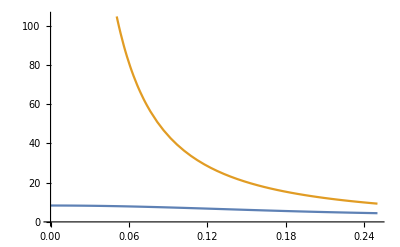

```mathematica
Plot[{Sum[1/(2 π r)(x (2/Max[x,0.005]-0.164414)^2) (Hypergeometric0F1[3,-(2/Max[x,0.005]-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.005]-0.164414) (x^2+r^2+2 x r)])(0.01),{x,0,2/0.164414,0.01}],(4 (-0.164414+2/r)^(3/2) HeavisideTheta[-0.164414+2/r])/(3 π)},{r,0,0.25}]
```

```mathematica
Table[Sum[1/(2 π r)(x (2/Max[x,0.005]-0.164414)^2) (Hypergeometric0F1[3,-(2/Max[x,0.005]-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.005]-0.164414) (x^2+r^2+2 x r)])(0.01),{x,0,2/0.164414,0.01}],{r,0,2,0.5}]
```

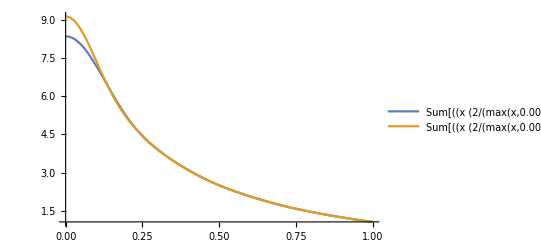

```mathematica
Plot[{Sum[1/(2 π r)(x (2/Max[x,0.005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.01),{x,0,2/0.164414,0.01}],Sum[1/(2 π r)(x (2/Max[x,0.005]-0.164414)^2) (Hypergeometric0F1[3,-(2/Max[x,0.005]-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.005]-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.164414,0.001}]},{r,0,1},PlotLegends->"Expressions"]
```

```mathematica
.
```

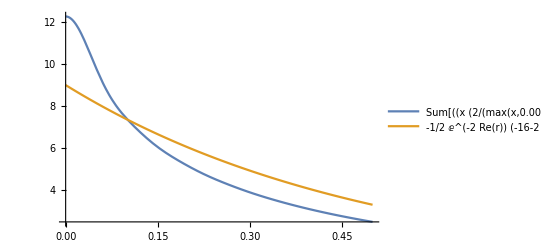

```mathematica
Plot[{Sum[1/(2 π r)(x (2/Max[x,0.0005]-0.164414)^2) (Hypergeometric0F1[3,-(2/Max[x,0.0005]-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.0005]-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.16,0.001}],-1/2 ⅇ^(-2 Re[r]) (-16-2 ⅇ^Re[r]-ⅇ^Re[r] Abs[r]^2+2 ⅇ^Re[r] Re[r])},{r,0,0.5},PlotLegends->"Expressions"]
```

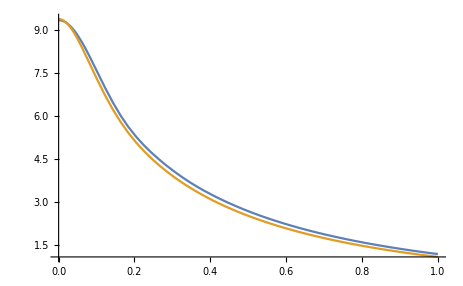

```mathematica
Plot[{Sum[1/(2 π r)(x (2/Max[x,0.005]-0.08)^2) (Hypergeometric0F1[3,-(2/Max[x,0.005]-0.08) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.005]-0.08) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.08,0.001}],Sum[1/(2 π r)(x (2/Max[x,0.005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.164414,0.001}]},{r,0,1}]
```

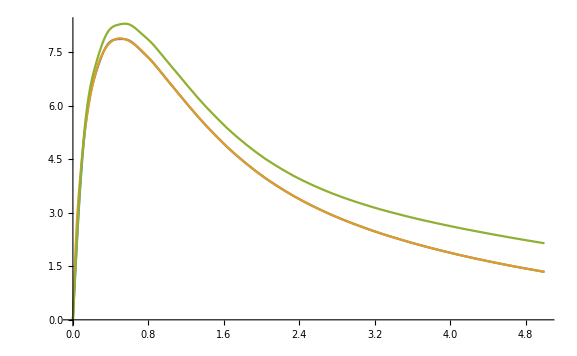

```mathematica
Plot[{Sum[(x (2/Max[x,0.005]-0.164414)^2) (Hypergeometric0F1[3,-(2/Max[x,0.005]-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.005]-0.164414) (x^2+r^2+2 x r)])(0.01),{x,0,2/0.164414,0.01}],Sum[(x (2/Max[x,0.0005]-0.164414)^2) (Hypergeometric0F1[3,-(2/Max[x,0.0005]-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.0005]-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.164414,0.001}],Sum[(x (2/Max[x,0.005]-0.1)^2) (Hypergeometric0F1[3,-(2/Max[x,0.005]-0.1) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.005]-0.1) (x^2+r^2+2 x r)])(0.01),{x,0,2/0.1,0.01}]},{r,0,5}]
```

```mathematica
Plot[{Sum[r/(2 π)(x (2/Max[x,0.005]-0.08)^2) (Hypergeometric0F1[3,-(2/Max[x,0.005]-0.08) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.005]-0.08) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.08,0.001}],Sum[r/(2 π)(x (2/Max[x,0.005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.164414,0.001}]},{r,0,10}]
```

Power::infy: Infinite expression 1/0. encountered.

$Aborted

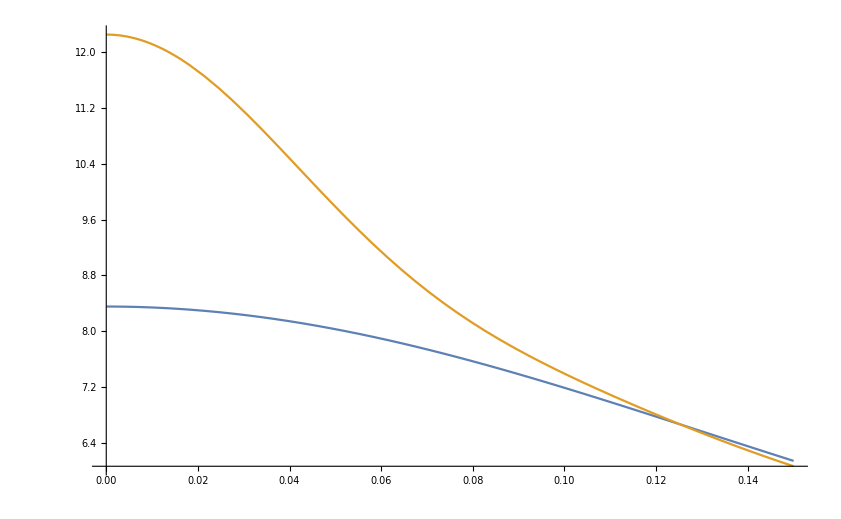

```mathematica
Plot[{Sum[(1/(2Pi r))(x (2/Max[x,0.005]-0.164414)^2) (Hypergeometric0F1[3,-(2/Max[x,0.005]-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.005]-0.164414) (x^2+r^2+2 x r)])(0.01),{x,0,2/0.164414,0.01}],Sum[(1/(2Pi r))(x (2/Max[x,0.0005]-0.164414)^2) (Hypergeometric0F1[3,-(2/Max[x,0.0005]-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.0005]-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.164414,0.001}]},{r,0,0.15}]
```

```mathematica
Limit[Sum[(1/(2Pi r))(x (2/(x+b)-0.164414)^2) (Hypergeometric0F1[3,-(2/(x+b)-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/(x+b)-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,(2/0.164414)-b,0.001}],b->0]
```

lim_(b→0) Sum[(0.000159155 x (-0.164414+2/(b+x))^2 (Hypergeometric0F1[3,(r^2-2 r x+x^2) (0.164414-2/(b+x))]-Hypergeometric0F1[3,(r^2+2 r x+x^2) (0.164414-2/(b+x))]))/r,{x,0,12.1644-b,0.001}]

```mathematica
(c-r)^6-(c+r)^6
```

(c-r)^6-(c+r)^6

```mathematica
Expand[(c-r)^6-(c+r)^6]
```

```mathematica
-12 c^5 r-40 c^3 r^3-12 c r^5
```

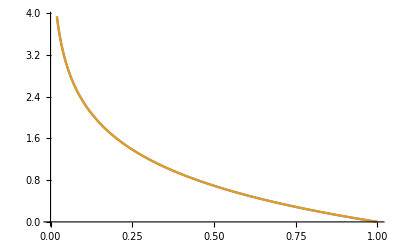

```mathematica
Plot[ {Log[E,1/x],-Log[E,x]},{x,0,1}]
```